```mathematica
(*Mathematica*)
```

```mathematica
T[n_,m_,d_]:=If[ n==m,2,If[(m==d&&n==d-2)||(n==d&&m==d-2),-1,If[(n==m-1 ||n==m+1)&&n<=d-1&&m<=d-1,-1,0]]]
m[d_]:=Table[T[n,m,d],{n,1,d},{m,1,d}]
```

```mathematica
m[4]
```

{{2,-1,0,0},{-1,2,-1,-1},{0,-1,2,0},{0,-1,0,2}}

```mathematica
(*D_4 Cartan Matrix*)
```

```mathematica
D4={{2,-1,0,0},
{-1,2,-1,-1},
{0,-1,2,0},
{0,-1,0,2}}
```

{{2,-1,0,0},{-1,2,-1,-1},{0,-1,2,0},{0,-1,0,2}}

```mathematica
Det[D4]
```

4

```mathematica
Tr[D4]
```

8

```mathematica
u[1]=N[Eigenvalues[D4]]
```

{3.73205,2.,2.,0.267949}

```mathematica
p[x_]=CharacteristicPolynomial[D4,x]
```

4-20 x+21 x^2-8 x^3+x^4

```mathematica
o[z_,1]=Integrate[p[x]^2,{x,-z,z}]
```

32 z+(1136 z^3)/3+(1538 z^5)/5+(212 z^7)/7+(2 z^9)/9

```mathematica
w[3]=z/.NSolve[o[z,1]-1==0,z]
```

{-0.0167817-0.303236 ⅈ,-0.0167817+0.303236 ⅈ,-0.0000264016-3.08543 ⅈ,-0.0000264016+3.08543 ⅈ,9.97449×10^-9-11.1961 ⅈ,9.97449×10^-9+11.1961 ⅈ,0.00135783-1.15026 ⅈ,0.00135783+1.15026 ⅈ,0.0309006}

```mathematica
r=N[(1+Sqrt[3]*I)/2]
```

0.5+0.866025 ⅈ

```mathematica
Abs[r]
```

1.

```mathematica
rc=-Conjugate[r]
```

-0.5+0.866025 ⅈ

```mathematica
D4c={{2,-r,0,0},
{-rc,2,-r,-r},
{0,-rc,2,0},
{0,-rc,0,2}}
```

{{2,-0.5-0.866025 ⅈ,0,0},{0.5-0.866025 ⅈ,2,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ},{0,0.5-0.866025 ⅈ,2,0},{0,0.5-0.866025 ⅈ,0,2}}

```mathematica
Det[D4c]
```

28.+1.48742×10^-17 ⅈ

```mathematica
Tr[D4c]
```

8

```mathematica
u[2]=N[Eigenvalues[D4c]]
```

{2.+1.73205 ⅈ,2.-1.73205 ⅈ,2.,2.-1.59595×10^-16 ⅈ}

```mathematica
q[x_]=CharacteristicPolynomial[D4c,x]//Chop
```

28.-44. x+27. x^2-8. x^3+x^4

```mathematica
o[z_,2]=Integrate[q[x]^2,{x,-z,z}]
```

0.+1568. z+2298.67 z^3+595.6 z^5+33.7143 z^7+0.222222 z^9

```mathematica
w[4]=z/.NSolve[o[z,2]-1==0,z]
```

{-0.000429827-0.931495 ⅈ,-0.000429827+0.931495 ⅈ,-9.12085×10^-6-3.82589 ⅈ,-9.12085×10^-6+3.82589 ⅈ,8.66689×10^-9-11.4891 ⅈ,8.66689×10^-9+11.4891 ⅈ,0.000120062-2.05154 ⅈ,0.000120062+2.05154 ⅈ,0.000637755}

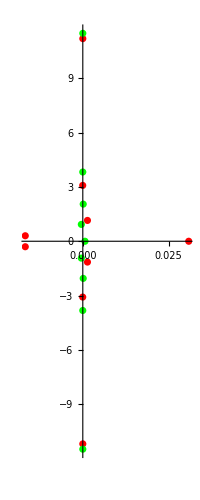

```mathematica
ComplexListPlot[{w[3],w[4]},PlotRange->All,PlotStyle->{Red,Green}]
```

```mathematica
w[1]=x/.NSolve[p[x]==0,x]
```

{0.267949,2.,2.,3.73205}

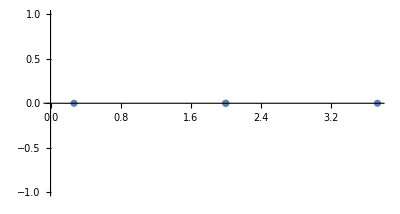

```mathematica
ComplexListPlot[w[1]]
```

```mathematica
w[2]=x/.NSolve[q[x]==0,x]
```

{2.,2.,2.-1.73205 ⅈ,2.+1.73205 ⅈ}

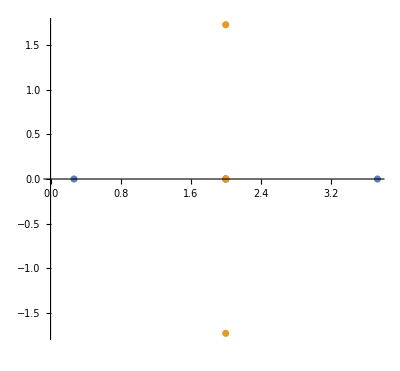

```mathematica
ComplexListPlot[{w[1],w[2]}]
```

```mathematica
D44c=D4.D4c
```

{{3.5+0.866025 ⅈ,-3.-1.73205 ⅈ,0.5+0.866025 ⅈ,0.5+0.866025 ⅈ},{-1.-1.73205 ⅈ,3.5+2.59808 ⅈ,-3.-1.73205 ⅈ,-3.-1.73205 ⅈ},{-0.5+0.866025 ⅈ,-1.-1.73205 ⅈ,4.5+0.866025 ⅈ,0.5+0.866025 ⅈ},{-0.5+0.866025 ⅈ,-1.-1.73205 ⅈ,0.5+0.866025 ⅈ,4.5+0.866025 ⅈ}}

```mathematica
Det[D44c]
```

112.+3.55271×10^-15 ⅈ

```mathematica
Tr[D44c]
```

16.+5.19615 ⅈ

```mathematica
u[3]=N[Eigenvalues[D44c]]
```

{7.27862+5.92543 ⅈ,4.12942-0.318883 ⅈ,4.-1.66533×10^-16 ⅈ,0.59196-0.410395 ⅈ}

```mathematica
s[x_]=CharacteristicPolynomial[D44c,x]//Chop
```

112.-(192.+83.1384 ⅈ) x+(89.+41.5692 ⅈ) x^2-(16.+5.19615 ⅈ) x^3+x^4

```mathematica
o[z_,3]=Integrate[s[x]^2,{x,-z,z}]
```

(0.+0. ⅈ)+25088. z+(33258.7+27491.1 ⅈ) z^3+(4678.8+4822.03 ⅈ) z^5+(116.286+71.2615 ⅈ) z^7+0.222222 z^9

```mathematica
o[z_,4]=Integrate[p[x]*q[z],{x,-z,z}]
```

224. z-352. z^2+608. z^3-680. z^4+397.2 z^5-129.6 z^6+24.8 z^7-3.2 z^8+(2 z^9)/5

```mathematica
w[5]=z/.NSolve[o[z,4]==0,z]
```

{0.,0.+0.762283 ⅈ,0.-0.762283 ⅈ,0.-5.86676 ⅈ,0.+5.86676 ⅈ,2.,2.,2.+1.73205 ⅈ,2.-1.73205 ⅈ}

```mathematica
w[6]=z/.NSolve[o[z,3]-1==0,z]
```

{-6.78388+22.7487 ⅈ,-0.981939+6.74609 ⅈ,-0.291846-0.737961 ⅈ,-0.151089-2.61198 ⅈ,0.0000398597-6.9395×10^-14 ⅈ,0.151092+2.61197 ⅈ,0.291803+0.737964 ⅈ,0.981939-6.74609 ⅈ,6.78388-22.7487 ⅈ}

```mathematica
(*root test as ones and zero*)
```

```mathematica
FullSimplify[Table[o[w[3][[j]],1],{j,Length[w[3]]}]]//Chop
```

{1.,1.,1.,1.,1.+2.23517×10^-7 ⅈ,1.-2.23517×10^-7 ⅈ,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[4][[j]],2],{j,Length[w[4]]}]]//Chop
```

{1.,1.,1.+1.60071×10^-10 ⅈ,1.-1.60071×10^-10 ⅈ,1.-1.98372×10^-7 ⅈ,1.+1.98372×10^-7 ⅈ,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[5][[j]],4],{j,Length[w[4]]}]]//Chop
```

{0,0,0,3.0268×10^-9+1.39698×10^-9 ⅈ,-5.82077×10^-10+4.65661×10^-10 ⅈ,0,0,0,0}

```mathematica
FullSimplify[Table[o[w[6][[j]],3],{j,Length[w[6]]}]]//Chop
```

{1.0001+0.000045944 ⅈ,1.+1.49012×10^-8 ⅈ,1.,1.-1.16415×10^-10 ⅈ,1.,1.-1.16415×10^-10 ⅈ,1.,1.+1.39698×10^-8 ⅈ,1.+0.000113403 ⅈ}

```mathematica
ph[x_,1]=x^2*q[x]/p[x]
```

(x^2 (28.-44. x+27. x^2-8. x^3+x^4))/(4-20 x+21 x^2-8 x^3+x^4)

```mathematica
ph[z_,2]=z^2*(o[z,2]-1)/(o[z,1]-1)
```

(z^2 (-1.+1568. z+2298.67 z^3+595.6 z^5+33.7143 z^7+0.222222 z^9))/(-1+32 z+(1136 z^3)/3+(1538 z^5)/5+(212 z^7)/7+(2 z^9)/9)

```mathematica
g1=JuliaSetPlot[ph[x,1]/N[2],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x,1]/N[2],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_D_4_Hermanrings_both.jpg",{g1,g2}]
```

Julia_D_4_Hermanrings_both.jpg

```mathematica
g3=ComplexPlot[ph[x,1],{z,-5-I*5,5+5*I},ColorFunction->"CyclicReImLogAbs",ImageSize->{2000,2000}];
```

```mathematica
g4=ComplexPlot3D[ph[x,1],{z,-5-I*5,5+5*I},ColorFunction->"CyclicReImLogAbs",ImageSize->{2000,2000}];
```

```mathematica
Export["D_4_Hermanrings_both_Complex_Plots.jpg",{g3,g4}]
```

D_4_Hermanrings_both_Complex_Plots.jpg

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
ph[x_]=(x^2 (28.-44.* x+27.*x^2-8. x^3+x^4))/(4-20 x+21 x^2-8 x^3+x^4)
```

(x^2 (28.-44. x+27. x^2-8. x^3+x^4))/(4-20 x+21 x^2-8 x^3+x^4)

```mathematica
w=x/.NSolve[ph[x]==0,x]//Chop
```

{2.-1.73205 ⅈ,2.+1.73205 ⅈ,0,0}

```mathematica
max=Max[Norm/@w]+1
```

3.64575

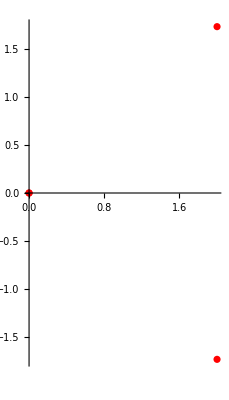

```mathematica
ComplexListPlot[w,PlotStyle->Red,ImageSize->Full]
```

```mathematica
ga=ComplexPlot3D[ph[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->4000];
```

```mathematica
Export["j_1000_hermanrings_Hermanring_D4_Polynomials_ComplexPlot_ga.jpg",ga]
```

j_1000_hermanrings_Hermanring_D4_Polynomials_ComplexPlot_ga.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Oct 2026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=ph[nz]/N[2];
        ++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.5+0.0001,3.5,1000},{-3.+0.001,3.,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→Hue,Background→Black,ViewPoint→Above,ImageSize->2*{2000,2000}];
```

```mathematica
Export["j_1000_hermanrings_D4_Polynomials_2Integrated2_In_Out_monitor_g1.jpg",g1]
```

j_1000_hermanrings_D4_Polynomials_2Integrated2_In_Out_monitor_g1.jpg

```mathematica
arraym=FractalPureM[{{-2.5+0.0001,3.5,2000},{-3.0+0.001,3.05,2000}}];
```

```mathematica
g2=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction->"Rainbow",ImageSize->2*{2000,2000},Frame->False];
```

```mathematica
Export["j_2000_hermanrings_D4_Polynomials_2Ingerated_In_Out_monitor_g2.jpg",g2]
```

j_2000_hermanrings_D4_Polynomials_2Ingerated_In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2*{2000,2000},Frame->False];
```

$Aborted

```mathematica
Export["j_1000_hermanrings_D4_Polynomials_In_Out_monitor_g3.jpg",g3]
```

```mathematica
Export["j_2000_hermanrings_D4_Polynomials_In_Out_monitor_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->8000]]
```

```mathematica
colortab=Reverse[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]]];
```

```mathematica
g3a=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2*{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_hermanrings_D4_Polynomials_In_Out_monitor_g3a.jpg",g3a]
```

```mathematica
Export["j_2000_hermanrings_D4_Polynomials2_In_Out_monitor_grid.jpg",GraphicsGrid[{{g2a,g2}, 
 {g3,g1}},ImageSize->8000]]
```

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
f[x_]=(x^2 (28.-44.* x+27.*x^2-8. x^3+x^4))/(4-20 x+21 x^2-8 x^3+x^4)
```

(x^2 (28.-44. x+27. x^2-8. x^3+x^4))/(4-20 x+21 x^2-8 x^3+x^4)

```mathematica
(*Mandelbrot with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Nov 2026 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 16) && (escapeCount < 511) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/2.;
		++escapeCount
	];
	escapeCount
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.6,3.6,1000},{-3.1,3.1,1000}}];
```

```mathematica
g1=ListPlot3D[Log[1/Max[arraym]+arraym], Mesh -> False,AspectRatio -> 1,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[Abs[Log[1+arraym]],Mesh -> False,AspectRatio -> 1,ColorFunction->"GreenPinkTones",ImageSize->2000,Frame->False];
```

```mathematica
g3=ListDensityPlot[arraym,Mesh -> False, AspectRatio -> 1, ColorFunction->"CMYKColors",ImageSize->2000,Frame->False];
```

```mathematica
g4=ListDensityPlot[arraym, Mesh -> False, AspectRatio -> 1,ColorFunction->(Hue[2#]&),ImageSize->2000,Axes->False,Frame->False];
```

```mathematica
g5=ListDensityPlot[Log[1/Max[arraym]+arraym],Mesh -> False, AspectRatio ->1, ColorFunction->(Hue[#/1.5]&),ImageSize->2000,Axes->False,Frame->False];
```

```mathematica
(*Fonction pour colorier des isocontours,exemple d'utilisation typique:ContourPlot[T[x,y],{x,-10,10},{y,-10,10},ColorFunction->cf]*)
(*http://perso.ensem.inpl-nancy.fr/Emmanuel.Plaut/mathematica/mycolorfunction.m*)
colortab=Reverse[{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}];

cf[l_]:=Block[{niv,rgb},niv=If[l<1/64,1,Ceiling[64 l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g6=ListDensityPlot[Log[1/Max[arraym]+arraym], Mesh -> False, AspectRatio -> 1, ColorFunction->cf,ImageSize->2000,Frame->False];
```

```mathematica
Export["j_1000_hermanrings_D4_Polynomial_grid.jpg",GraphicsGrid[{{g1,g2}, 
 {g3,g4},{g5,g6}},ImageSize->{4000,6000}]]
```

j_1000_hermanrings_D4_Polynomial_grid.jpg

```mathematica
(*end*)
```